# Лабораторная работа №3. Структура выражения

Выполнила студентка ММФ БГУ 
КМ, 1 к, 5 гр. Бельская Е.А.
      16 сентября 2019

## 1. Построение дерева выражения

### Задание 1.1

```mathematica
-1/5+ⅇ+(1-2ⅈ)/(-.4x+3y)-7πxz+z^(6x)
```

```mathematica
(a^2+b^2)/((a+x)(b^2+x^2))
```

### Задание 1.2

```mathematica
-1/5+ⅇ+(1-2ⅈ)/(-.4x+3y)-7πxz+z^(6x)//FullForm
```

Plus[Rational[-1,5],E,Times[Complex[1,-2],Power[Plus[Times[-0.4,x],Times[3,y]],-1]],Power[z,Times[6,x]],Times[-7,\[Pi]xz]]

```mathematica
(a^2+b^2)/((a+x)(b^2+x^2))//FullForm
```

Times[Plus[Power[a,2],Power[b,2]],Power[Plus[a,x],-1],Power[Plus[Power[b,2],Power[x,2]],-1]]

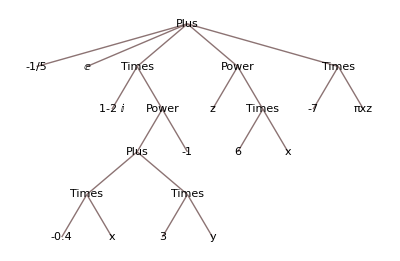

```mathematica
-1/5+ⅇ+(1-2ⅈ)/(-.4x+3y)-7πxz+z^(6x)//TreeForm
```

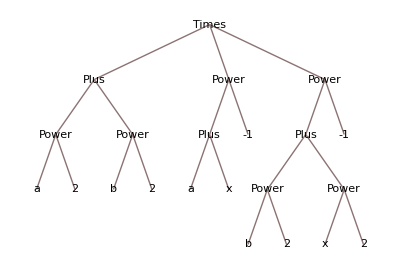

```mathematica
(a^2+b^2)/((a+x)(b^2+x^2))//TreeForm
```

```mathematica
expr1=-1/5+ⅇ+(1-2ⅈ)/(-.4x+3y)-7πxz+z^(6x)
```

-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz

```mathematica
myExpr=(a^2+b^2)/((a+x)(b^2+x^2))
```

(a^2+b^2)/((a+x) (b^2+x^2))

```mathematica
?expr1
```

Global`expr1

expr1=-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz

```mathematica
?myExpr
```

Global`myExpr

myExpr=(a^2+b^2)/((a+x) (b^2+x^2))

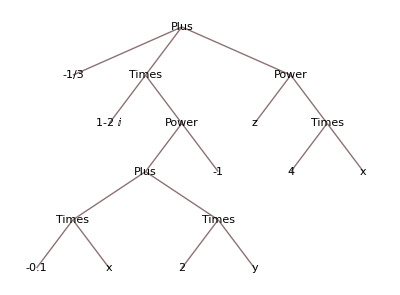

```mathematica
(1-2ⅈ)/(2y-.1x)-1/3+z^(4x)//TreeForm
```

Не отличатся (баги устранены)

## 2. Анализ структуры выражения

### Задание 2.1

```mathematica
-1/5+ⅇ+(1-2ⅈ)/(-.4x+3y)-7πxz+z^(6x)
```

```mathematica
(a^2+b^2)/((a+x)(b^2+x^2))
```

```mathematica
?expr1
```

Global`expr1

expr1=-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz

```mathematica
?myExpr
```

Global`myExpr

myExpr=(a^2+b^2)/((a+x) (b^2+x^2))

```mathematica
myExpr//TreeForm
```

-Graphics-

```mathematica
expr1//TreeForm
```

-Graphics-

Чтобы извлечь из выражения expr все подвыражения определенного уровня, используют функцию Level[expr, levelspec]. Она возвращает список подвыражений выражения expr, находящихся на указанных уровнях. 
        Количество уровней выражения  expr вычисляет функция Depth[expr]. Все возможные подвыражения выражения расположены на уровнях от 0 до Depth[expr]-1.

```mathematica
Level[expr1, {0}]
```

{-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz}

```mathematica
Level[expr1, {1}]
```

{-1/5,ⅇ,(1-2 ⅈ)/(-0.4 x+3 y),z^(6 x),-7 πxz}

```mathematica
Level[expr1, {2}]
```

{1-2 ⅈ,1/(-0.4 x+3 y),z,6 x,-7,πxz}

```mathematica
Level[expr1, {3}]
```

{-0.4 x+3 y,-1,6,x}

```mathematica
Level[expr1, {4}]
```

{-0.4 x,3 y}

```mathematica
Level[expr1, {5}]
```

{-0.4,x,3,y}

На 0 уровне находится само выражение. Возвращает выражение типа

```mathematica
Depth[expr1]
```

6

```mathematica
Depth[expr1]-1
```

5

```mathematica
Level[expr1, {6}]
```

{}

Максимальное n, при котором вычисленное выражение Level[expr1, {n}] возращает непустой список - Depth[expr1] - 1

```mathematica
Level[expr1, {Depth[expr1]-1}]
```

{-0.4,x,3,y}

```mathematica
Level[expr1, {-1}]
```

{-1/5,ⅇ,1-2 ⅈ,-0.4,x,3,y,-1,z,6,x,-7,πxz}

```mathematica
Level[expr1, {Depth[expr1]-2}]
```

{-0.4 x,3 y}

```mathematica
Level[expr1, {-2}]
```

{-0.4 x,3 y,6 x,-7 πxz}

Результаты:

### Задание 2.2

```mathematica
Table[Level[expr1,{i}],{i,0, Depth[expr1]-1}]//MatrixForm
```

({-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz}
{-1/5,ⅇ,(1-2 ⅈ)/(-0.4 x+3 y),z^(6 x),-7 πxz}
{1-2 ⅈ,1/(-0.4 x+3 y),z,6 x,-7,πxz}
{-0.4 x+3 y,-1,6,x}
{-0.4 x,3 y}
{-0.4,x,3,y})

```mathematica
Head/@Level[expr1,{0}]
```

{Plus}

```mathematica
Head/@Level[expr1,{1}]
```

{Rational,Symbol,Times,Power,Times}

```mathematica
Head/@Level[expr1,{2}]
```

{Complex,Power,Symbol,Times,Integer,Symbol}

```mathematica
Head/@Level[expr1,{3}]
```

{Plus,Integer,Integer,Symbol}

```mathematica
Head/@Level[expr1,{4}]
```

{Times,Times}

```mathematica
Head/@Level[expr1,{5}]
```

{Real,Symbol,Integer,Symbol}

Определяет голову подвыражения на определённом подуровне

```mathematica
Table[Head/@Level[expr1,{i}],{i,0, Depth[expr1]-1}]//MatrixForm
```

({Plus}
{Rational,Symbol,Times,Power,Times}
{Complex,Power,Symbol,Times,Integer,Symbol}
{Plus,Integer,Integer,Symbol}
{Times,Times}
{Real,Symbol,Integer,Symbol})

```mathematica
Table[{Head[#],#}&/@Level[expr1,{i}],{i,0, Depth[expr1]-1}]//MatrixForm
```

({{Plus,-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz}}
{{Rational,-1/5},{Symbol,ⅇ},{Times,(1-2 ⅈ)/(-0.4 x+3 y)},{Power,z^(6 x)},{Times,-7 πxz}}
{{Complex,1-2 ⅈ},{Power,1/(-0.4 x+3 y)},{Symbol,z},{Times,6 x},{Integer,-7},{Symbol,πxz}}
{{Plus,-0.4 x+3 y},{Integer,-1},{Integer,6},{Symbol,x}}
{{Times,-0.4 x},{Times,3 y}}
{{Real,-0.4},{Symbol,x},{Integer,3},{Symbol,y}})

```mathematica
Table[{Head[#],#}&/@Level[expr1,{0}]]//MatrixForm
```

(Plus | -1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz)

```mathematica
Table[{Head[#],#}&/@Level[expr1,{1}]]//MatrixForm
```

(Rational | -1/5
Symbol | ⅇ
Times | (1-2 ⅈ)/(-0.4 x+3 y)
Power | z^(6 x)
Times | -7 πxz)

```mathematica
Table[{Head[#],#}&/@Level[expr1,{2}]]//MatrixForm
```

(Complex | 1-2 ⅈ
Power | 1/(-0.4 x+3 y)
Symbol | z
Times | 6 x
Integer | -7
Symbol | πxz)

```mathematica
Table[{Head[#],#}&/@Level[expr1,{3}]]//MatrixForm
```

(Plus | -0.4 x+3 y
Integer | -1
Integer | 6
Symbol | x)

```mathematica
Table[{Head[#],#}&/@Level[expr1,{4}]]//MatrixForm
```

(Times | -0.4 x
Times | 3 y)

```mathematica
Table[{Head[#],#}&/@Level[expr1,{5}]]//MatrixForm
```

(Real | -0.4
Symbol | x
Integer | 3
Symbol | y)

### Задание 2.3

```mathematica
Position[expr1,x]
```

{{3,2,1,1,2},{4,2,2}}

```mathematica
Position[expr1,y]
```

{{3,2,1,2,2}}

```mathematica
Position[expr1,z]
```

{{4,1}}

Выводит расположение подвыражений, содержащих определяемый элемент

```mathematica
Part[expr1,4;;5]
```

z^(6 x)-7 πxz

Извлечение части выражения(аргументов) в соответствии с указанной позицией

```mathematica
Take[expr1,{-2,-1}]
```

z^(6 x)-7 πxz

Извлекает список элементов с указанной позицией

```mathematica
AtomQ[expr1]
```

False

Проверяет содержит ли выражение атомарные объекты

```mathematica
AtomQ/@Level[expr1,{2}]
```

{True,False,True,False,True,True}

Проверяет содержит ли выражение атомарные объекты на конкретном уровне

## 3. Разложение выражения по уровням

### Задание 3.1

```mathematica
myExprLevels[expr_]:=Do[Print[MatrixForm[{Head[#],#}]&/@Level [expr, {i}]], {i, 0, Depth[expr1]-1}]
```

```mathematica
myExprLevels[myExpr]
```

{(Times
(a^2+b^2)/((a+x) (b^2+x^2)))}

{(Plus
a^2+b^2),(Power
1/(a+x)),(Power
1/(b^2+x^2))}

{(Power
a^2),(Power
b^2),(Plus
a+x),(Integer
-1),(Plus
b^2+x^2),(Integer
-1)}

{(Symbol
a),(Integer
2),(Symbol
b),(Integer
2),(Symbol
a),(Symbol
x),(Power
b^2),(Power
x^2)}

{(Symbol
b),(Integer
2),(Symbol
x),(Integer
2)}

### Задание 3.2

```mathematica
myExprLevels[expr1]
```

{(Plus
-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)+z^(6 x)-7 πxz)}

{(Rational
-1/5),(Symbol
ⅇ),(Times
(1-2 ⅈ)/(-0.4 x+3 y)),(Power
z^(6 x)),(Times
-7 πxz)}

{(Complex
1-2 ⅈ),(Power
1/(-0.4 x+3 y)),(Symbol
z),(Times
6 x),(Integer
-7),(Symbol
πxz)}

{(Plus
-0.4 x+3 y),(Integer
-1),(Integer
6),(Symbol
x)}

{(Times
-0.4 x),(Times
3 y)}

{(Real
-0.4),(Symbol
x),(Integer
3),(Symbol
y)}

```mathematica
MatrixForm[Position[expr1,#]&/@Level[expr1, {-1}],TableHeadings->{Level[expr1,{-1}],None}]
```

(-1/5 | {{1}}
ⅇ | {{2}}
1-2 ⅈ | {{3,1}}
-0.4 | {{3,2,1,1,1}}
x | {{3,2,1,1,2},{4,2,2}}
3 | {{3,2,1,2,1}}
y | {{3,2,1,2,2}}
-1 | {{3,2,2}}
z | {{4,1}}
6 | {{4,2,1}}
x | {{3,2,1,1,2},{4,2,2}}
-7 | {{5,1}}
πxz | {{5,2}})

## 4.

```mathematica
MyExpr=(x-5)^(1/2)+33π*√(13 x^4)+ⅇ
```

ⅇ+√(-5+x)+33 √13 π √(x^4)

```mathematica
Maximize[MyExpr,{x}]
```

Maximize::natt: The maximum is not attained at any point satisfying the given constraints.

{∞,{x→∞}}

```mathematica
?MyExpr
```

Global`MyExpr

MyExpr=ⅇ+√(-5+x)+33 √13 π √(x^4)

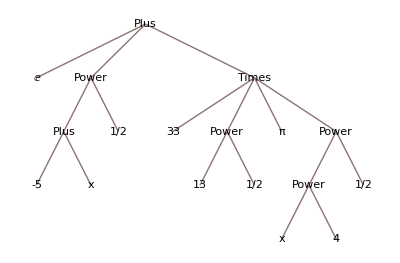

```mathematica
TreeForm[MyExpr]
```

```mathematica
Level[MyExpr,1]
```

{ⅇ,√(-5+x),33 √13 π √(x^4)}

```mathematica
Level[MyExpr,2]
```

{ⅇ,-5+x,1/2,√(-5+x),33,√13,π,√(x^4),33 √13 π √(x^4)}

```mathematica
Level[MyExpr,3]
```

{ⅇ,-5,x,-5+x,1/2,√(-5+x),33,13,1/2,√13,π,x^4,1/2,√(x^4),33 √13 π √(x^4)}

```mathematica
Level[MyExpr,4]
```

{ⅇ,-5,x,-5+x,1/2,√(-5+x),33,13,1/2,√13,π,x,4,x^4,1/2,√(x^4),33 √13 π √(x^4)}

```mathematica
Depth[MyExpr]
```

5

```mathematica
Level[MyExpr,{4}]
```

{x,4}

```mathematica
Level[MyExpr,{5}]
```

{}

```mathematica
Level[MyExpr,{1}]
```

{ⅇ,√(-5+x),33 √13 π √(x^4)}

```mathematica
Level[MyExpr,{2}]
```

{-5+x,1/2,33,√13,π,√(x^4)}

```mathematica
Level[MyExpr,{Depth[MyExpr]-1}]
```

{x,4}

```mathematica
Level[MyExpr,{-1}]
```

{ⅇ,-5,x,1/2,33,13,1/2,π,x,4,1/2}

```mathematica
Level[MyExpr,{Depth[MyExpr]-2}]
```

{-5,x,13,1/2,x^4,1/2}

```mathematica
Level[MyExpr,{-2}]
```

{√2,x^4,11+x}

```mathematica
Table[Level[MyExpr,{i}],{i,0,Depth[MyExpr]-1}]
```

{{ⅇ+√(-5+x)+33 √13 π √(x^4)},{ⅇ,√(-5+x),33 √13 π √(x^4)},{-5+x,1/2,33,√13,π,√(x^4)},{-5,x,13,1/2,x^4,1/2},{x,4}}

```mathematica
Table[Level[MyExpr,{i}],{i,0,Depth[MyExpr]-1}]//MatrixForm
```

({ⅇ+√(-5+x)+33 √13 π √(x^4)}
{ⅇ,√(-5+x),33 √13 π √(x^4)}
{-5+x,1/2,33,√13,π,√(x^4)}
{-5,x,13,1/2,x^4,1/2}
{x,4})

```mathematica
Head/@Level[MyExpr,{0}]
```

{Plus}

```mathematica
Head/@Level[MyExpr,{1}]
```

{Symbol,Power,Times}

```mathematica
Head/@Level[MyExpr,{2}]
```

{Plus,Rational,Integer,Power,Symbol,Power}

```mathematica
Head/@Level[MyExpr,{3}]
```

{Integer,Symbol,Integer,Rational,Power,Rational}

```mathematica
Head/@Level[MyExpr,{4}]
```

{Symbol,Integer}

```mathematica
Table[Head/@Level[MyExpr,{i}],{i,0, Depth[MyExpr]-1}]//MatrixForm
```

({Plus}
{Symbol,Power,Times}
{Plus,Rational,Integer,Power,Symbol,Power}
{Integer,Symbol,Integer,Rational,Power,Rational}
{Symbol,Integer})

```mathematica
Table[{Head[#],#}&/@Level[MyExpr,{i}],{i,0, Depth[MyExpr]-1}]
```

{{{Plus,ⅇ+√(-5+x)+33 √13 π √(x^4)}},{{Symbol,ⅇ},{Power,√(-5+x)},{Times,33 √13 π √(x^4)}},{{Plus,-5+x},{Rational,1/2},{Integer,33},{Power,√13},{Symbol,π},{Power,√(x^4)}},{{Integer,-5},{Symbol,x},{Integer,13},{Rational,1/2},{Power,x^4},{Rational,1/2}},{{Symbol,x},{Integer,4}}}

```mathematica
Table[{Head[#],#}&/@Level[MyExpr,{i}],{i,0, Depth[MyExpr]-1}]//MatrixForm
```

({{Plus,ⅇ+√(-5+x)+33 √13 π √(x^4)}}
{{Symbol,ⅇ},{Power,√(-5+x)},{Times,33 √13 π √(x^4)}}
{{Plus,-5+x},{Rational,1/2},{Integer,33},{Power,√13},{Symbol,π},{Power,√(x^4)}}
{{Integer,-5},{Symbol,x},{Integer,13},{Rational,1/2},{Power,x^4},{Rational,1/2}}
{{Symbol,x},{Integer,4}})

```mathematica
Table[{Head[#],#}&/@Level[MyExpr,{1}]]//MatrixForm
```

(Symbol | ⅇ
Power | √(-5+x)
Times | 33 √13 π √(x^4))

```mathematica
Table[{Head[#],#}&/@Level[MyExpr,{2}]]//MatrixForm
```

(Plus | -5+x
Rational | 1/2
Integer | 33
Power | √13
Symbol | π
Power | √(x^4))

```mathematica
Table[{Head[#],#}&/@Level[MyExpr,{3}]]//MatrixForm
```

(Integer | -5
Symbol | x
Integer | 13
Rational | 1/2
Power | x^4
Rational | 1/2)

```mathematica
Table[{Head[#],#}&/@Level[MyExpr,{4}]]//MatrixForm
```

(Symbol | x
Integer | 4)

```mathematica
Table[{Head[#],#}&/@Level[MyExpr,{i}],{i,0, Depth[MyExpr]-1}]//MatrixForm
```

({{Plus,ⅇ+√(-5+x)+33 √13 π √(x^4)}}
{{Symbol,ⅇ},{Power,√(-5+x)},{Times,33 √13 π √(x^4)}}
{{Plus,-5+x},{Rational,1/2},{Integer,33},{Power,√13},{Symbol,π},{Power,√(x^4)}}
{{Integer,-5},{Symbol,x},{Integer,13},{Rational,1/2},{Power,x^4},{Rational,1/2}}
{{Symbol,x},{Integer,4}})

```mathematica
Position[MyExpr, x]
```

{{2,1,2},{3,4,1,1}}

```mathematica
Length[MyExpr]
```

3

```mathematica
Part[MyExpr,{1}]
```

ⅇ

```mathematica
Part[Level[MyExpr,{2}],{5}]
```

{π}

```mathematica
Take[MyExpr,{-2,-1}]
```

√(-5+x)+33 √13 π √(x^4)

```mathematica
AtomQ[MyExpr]
```

False